```mathematica
ClearAll[g,v,av];
```

```mathematica
n=4;
l=6;
```

```mathematica
Do[
Do[


v=6;
p=0.1;

vv=ToString[v];
ll=ToString[l];
pp=ToString[p];
nn=ToString[n];

g[l][v][n]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/GapD-l"<>ll<>"k-v"<>vv<>"-p"<>pp<>"-"<>nn<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number}];
ve[l][v][n]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/velD-l"<>ll<>"k-v"<>vv<>"-p"<>pp<>"-"<>nn<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number}];
av[l][v][n]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/AveVel-l"<>ll<>"k-v"<>vv<>"-p"<>pp<>"-"<>nn<>".txt",{Number,Number,Number,Number}];



ngap="2";
nvel="2";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;
gap[l][v][n]=Table[{g[l][v][n][[All,1]][[j]],Sum[g[l][v][n][[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g[l][v][n]]}];
vel[l][v][n]=Table[{ve[l][v][n][[All,1]][[j]],Sum[ve[l][v][n][[All,i]][[j]],{i,3,nv+2}]},{j,1,Length[ve[l][v][n]]}];
avel[l][v][n]=Table[{av[l][v][n][[All,1]][[j]],av[l][v][n][[All,2]][[j]]},{j,1,Length[av[l][v][n]]}];
,{n,{1,2,3,4}}];
,{l,{2,5,10,20,30}}];
```

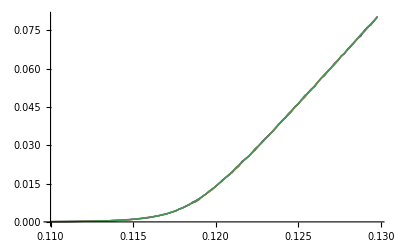

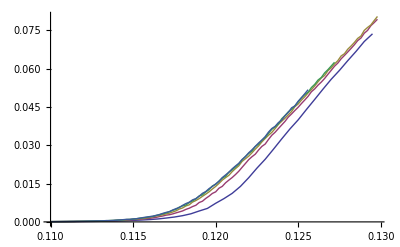

```mathematica
v=6;
l=10;
n=1;
ListLinePlot[{gap[l][v][1],gap[l][v][2],gap[l][v][3],gap[l][v][4]}]
ListLinePlot[{gap[2][v][n],gap[5][v][n],gap[10][v][n],gap[20][v][n],gap[30][v][n]}]
```

```mathematica
Do[
Do[


v=6;
p=0.1;

vv=ToString[v];
ll=ToString[l];
pp=ToString[p];
nn=ToString[n];

g[l][v][n]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/GapD-l"<>ll<>"k-v"<>vv<>"-p"<>pp<>"-"<>nn<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
ve[l][v][n]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/velD-l"<>ll<>"k-v"<>vv<>"-p"<>pp<>"-"<>nn<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av[l][v][n]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/AveVel-l"<>ll<>"k-v"<>vv<>"-p"<>pp<>"-"<>nn<>".txt",{Number,Number,Number,Number}];



ngap="5";
nvel="5";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;
gap[l][v][n]=Table[{g[l][v][n][[All,1]][[j]],Sum[g[l][v][n][[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g[l][v][n]]}];
vel[l][v][n]=Table[{ve[l][v][n][[All,1]][[j]],Sum[ve[l][v][n][[All,i]][[j]],{i,3,nv+2}]},{j,1,Length[ve[l][v][n]]}];
avel[l][v][n]=Table[{av[l][v][n][[All,1]][[j]],av[l][v][n][[All,2]][[j]]},{j,1,Length[av[l][v][n]]}];
,{n,{1,2,3,4}}];
,{l,{2,5,10,20,30}}];
```

7

4

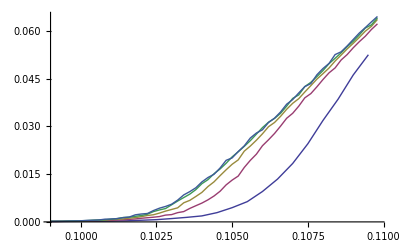

```mathematica
v=7
n=4
ListLinePlot[{gap[2][v][n],gap[5][v][n],gap[10][v][n],gap[20][v][n],gap[30][v][n]}]
```

```mathematica
ClearAll[gs,ig,d0,val,bf,βf,minf,maxf,g]
```

Vmax = 5:

Value:  0.00819053  0.00820727  0.00824393  0.00828618

b:  0.07  0.07  0.07  0.07

β:  -0.32  -0.325  -0.33  -0.32

For n = 1:

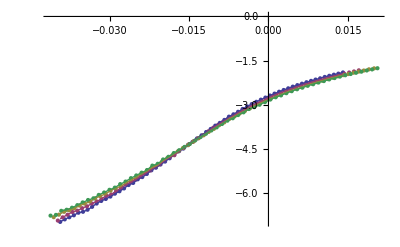

For n = 2:

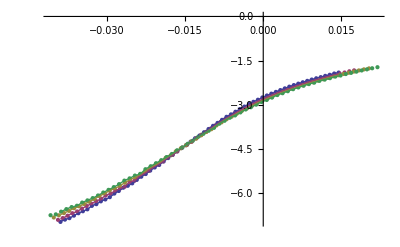

For n = 3:

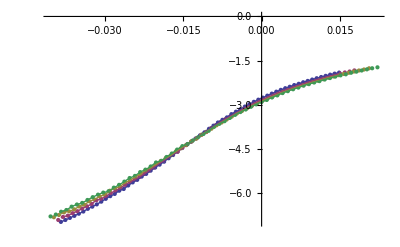

For n = 4:

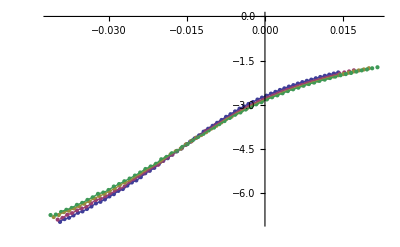

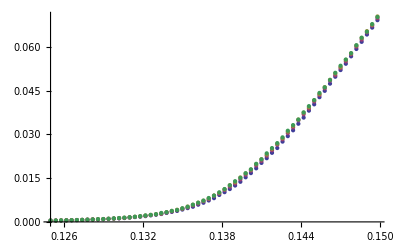

```mathematica
Do[

v=5;

d0[5]=0.13868040135702742;
d0[6]=0.11675839124676939;
d0[7]=0.10129517685639909;
d0[8]=0.08925417883112817;
d0[9]=0.081;
d0[11]=0.06576996509783684;
α=0.09;
z=0.09;
val[v][n]=1000;


(*n=1;*)

g[5][v]=gap[5][v][n];
g[10][v]=gap[10][v][n];
g[20][v]=gap[20][v][n];
g[30][v]=gap[30][v][n];


l1=5;
l2=10;
l3=20;
l4=30;

For[b=0,b<0.2,b+=0.01,
For[β=-0.7,β<-0.3,β+=0.005,
Do[
gs[l][v]=Table[{(g[l][v][[All,1]][[i]]-d0[v]-b*(l*1000)^β)*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
ig[l][v]=Interpolation[gs[l][v]];
,{l,{l1,l2,l3,l4}}
];
min=Max[gs[l1][v][[All,1]][[1]],gs[l2][v][[All,1]][[1]],gs[l3][v][[All,1]][[1]],gs[l4][v][[All,1]][[1]]];
max=Min[gs[l1][v][[All,1]][[Length[gs[l1][v]]]],gs[l2][v][[All,1]][[Length[gs[l2][v]]]],gs[l3][v][[All,1]][[Length[gs[l3][v]]]],gs[l4][v][[All,1]][[Length[gs[l4][v]]]]];
delta=(max-min)/50;
int=Sum[delta*(Max[ig[l1][v][min+k*delta],ig[l2][v][min+k*delta],ig[l3][v][min+k*delta],ig[l4][v][min+k*delta]]-Min[ig[l1][v][min+k*delta],ig[l2][v][min+k*delta],ig[l3][v][min+k*delta],ig[l4][v][min+k*delta]]),{k,0,50}];
If[int<val[v][n],
val[v][n]=int;
bf[v][n]=b;
βf[v][n]=β;
minf[v][n]=min;
maxf[v][n]=max;
]
]
]

Do[
gsf[l][v][n]=Table[{(g[l][v][[All,1]][[i]]-d0[v]-bf[v][n]*(l*1000)^βf[v][n])*(l*1000)^z,Log[g[l][v][[All,2]][[i]]]+α*Log[1000*l]},{i,1,Length[g[l][v]]}];
igf[l][v][n]=Interpolation[gsf[l][v][n]];
,{l,{l1,l2,l3,l4}}];

,{n,{1,2,3,4}}]
Print["Vmax = ",v,": "]
Print[ "Value:  ",val[v][1],"  ",val[v][2],"  ",val[v][3],"  ",val[v][4]]  
Print[ "b:  ",bf[v][1],"  ",bf[v][2],"  ",bf[v][3],"  ",bf[v][4]]
Print[ "β:  ",βf[v][1],"  ",βf[v][2],"  ",βf[v][3],"  ",βf[v][4]]
n=1;
Print["For n = ",n,":"]
pic1=ListPlot[{gsf[l1][v][n],gsf[l2][v][n],gsf[l3][v][n],gsf[l4][v][n]}];
pic2=Plot[{igf[l1][v][n][x],igf[l2][v][n][x],igf[l3][v][n][x],igf[l4][v][n][x]},{x,minf[v][n],maxf[v][n]}];
Show[{pic1,pic2}]
n=2;
Print["For n = ",n,":"]
pic1=ListPlot[{gsf[l1][v][n],gsf[l2][v][n],gsf[l3][v][n],gsf[l4][v][n]}];
pic2=Plot[{igf[l1][v][n][x],igf[l2][v][n][x],igf[l3][v][n][x],igf[l4][v][n][x]},{x,minf[v][n],maxf[v][n]}];
Show[{pic1,pic2}]
n=3;
Print["For n = ",n,":"]
pic1=ListPlot[{gsf[l1][v][n],gsf[l2][v][n],gsf[l3][v][n],gsf[l4][v][n]}];
pic2=Plot[{igf[l1][v][n][x],igf[l2][v][n][x],igf[l3][v][n][x],igf[l4][v][n][x]},{x,minf[v][n],maxf[v][n]}];
Show[{pic1,pic2}]
n=4;
Print["For n = ",n,":"]
pic1=ListPlot[{gsf[l1][v][n],gsf[l2][v][n],gsf[l3][v][n],gsf[l4][v][n]}];
pic2=Plot[{igf[l1][v][n][x],igf[l2][v][n][x],igf[l3][v][n][x],igf[l4][v][n][x]},{x,minf[v][n],maxf[v][n]}];
Show[{pic1,pic2}]
ListPlot[{gap[5][v][n],gap[10][v][n],gap[20][v][n],gap[30][v][n]}]
```

```mathematica
v=5;
Print["Vmax = ",v,": "]
Print[ "Value:  ",val[v][1],"  ",val[v][2],"  ",val[v][3],"  ",val[v][4]]  
Print[ "b:  ",bf[v][1],"  ",bf[v][2],"  ",bf[v][3],"  ",bf[v][4]]
Print[ "β:  ",βf[v][1],"  ",βf[v][2],"  ",βf[v][3],"  ",βf[v][4]]
v=6;
Print["Vmax = ",v,": "]
Print[ "Value:  ",val[v][1],"  ",val[v][2],"  ",val[v][3],"  ",val[v][4]]  
Print[ "b:  ",bf[v][1],"  ",bf[v][2],"  ",bf[v][3],"  ",bf[v][4]]
Print[ "β:  ",βf[v][1],"  ",βf[v][2],"  ",βf[v][3],"  ",βf[v][4]]
v=7;
Print["Vmax = ",v,": "]
Print[ "Value:  ",val[v][1],"  ",val[v][2],"  ",val[v][3],"  ",val[v][4]]  
Print[ "b:  ",bf[v][1],"  ",bf[v][2],"  ",bf[v][3],"  ",bf[v][4]]
Print[ "β:  ",βf[v][1],"  ",βf[v][2],"  ",βf[v][3],"  ",βf[v][4]]
v=8;
Print["Vmax = ",v,": "]
Print[ "Value:  ",val[v][1],"  ",val[v][2],"  ",val[v][3],"  ",val[v][4]]  
Print[ "b:  ",bf[v][1],"  ",bf[v][2],"  ",bf[v][3],"  ",bf[v][4]]
Print[ "β:  ",βf[v][1],"  ",βf[v][2],"  ",βf[v][3],"  ",βf[v][4]]
v=9 ;
Print["Vmax = ",v,": "]
Print[ "Value:  ",val[v][1],"  ",val[v][2],"  ",val[v][3],"  ",val[v][4]]  
Print[ "b:  ",bf[v][1],"  ",bf[v][2],"  ",bf[v][3],"  ",bf[v][4]]
Print[ "β:  ",βf[v][1],"  ",βf[v][2],"  ",βf[v][3],"  ",βf[v][4]]
v=11 ;
Print["Vmax = ",v,": "]
Print[ "Value:  ",val[v][1],"  ",val[v][2],"  ",val[v][3],"  ",val[v][4]]  
Print[ "b:  ",bf[v][1],"  ",bf[v][2],"  ",bf[v][3],"  ",bf[v][4]]
Print[ "β:  ",βf[v][1],"  ",βf[v][2],"  ",βf[v][3],"  ",βf[v][4]]
```

Vmax = 5:

Value:  0.00819053  0.00820727  0.00824393  0.00828618

b:  0.07  0.07  0.07  0.07

β:  -0.32  -0.325  -0.33  -0.32

Vmax = 6:

Value:  0.00662344  0.00615601  0.00612335  0.0064724

b:  0.18  0.18  0.19  0.06

β:  -0.54  -0.535  -0.545  -0.365

Vmax = 7:

Value:  0.00364656  0.00408817  0.00341567  0.00371106

b:  0.19  0.19  0.19  0.19

β:  -0.56  -0.56  -0.555  -0.56

Vmax = 8:

Value:  0.00683855  0.00688766  0.00618268  0.00635753

b:  0.19  0.16  0.18  0.18

β:  -0.545  -0.52  -0.545  -0.545

Vmax = 9:

Value:  0.00782576  0.00731812  0.00767035  0.00647457

b:  0.19  0.19  0.07  0.19

β:  -0.49  -0.5  -0.32  -0.505

Vmax = 11:

Value:  0.0176454  0.00968919  0.0162366  0.0119822

b:  0.18  0.07  0.17  0.18

β:  -0.51  -0.325  -0.465  -0.48

Vmax = 7:

Value:  0.00364656  0.00408817  0.00341567  0.00371106

b:  0.19  0.19  0.19  0.19

β:  -0.56  -0.56  -0.555  -0.56

For n = 1:

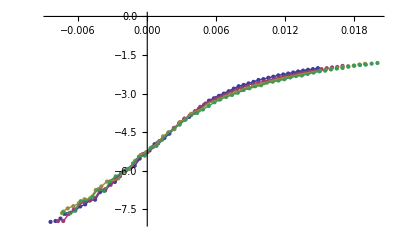

For n = 2:

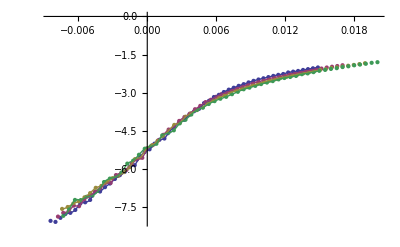

For n = 3:

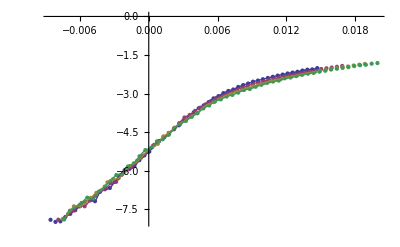

For n = 4:

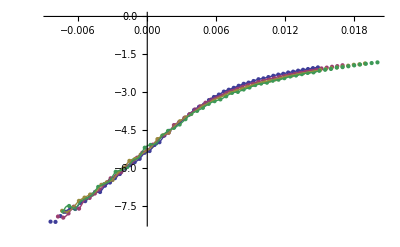

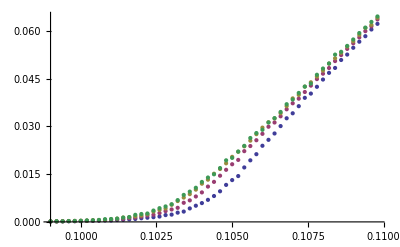

```mathematica
v=7;
Print["Vmax = ",v,": "]
Print[ "Value:  ",val[v][1],"  ",val[v][2],"  ",val[v][3],"  ",val[v][4]]  
Print[ "b:  ",bf[v][1],"  ",bf[v][2],"  ",bf[v][3],"  ",bf[v][4]]
Print[ "β:  ",βf[v][1],"  ",βf[v][2],"  ",βf[v][3],"  ",βf[v][4]]
n=1;
Print["For n = ",n,":"]
pic1=ListPlot[{gsf[l1][v][n],gsf[l2][v][n],gsf[l3][v][n],gsf[l4][v][n]}];
pic2=Plot[{igf[l1][v][n][x],igf[l2][v][n][x],igf[l3][v][n][x],igf[l4][v][n][x]},{x,minf[v][n],maxf[v][n]}];
Show[{pic1,pic2}]
n=2;
Print["For n = ",n,":"]
pic1=ListPlot[{gsf[l1][v][n],gsf[l2][v][n],gsf[l3][v][n],gsf[l4][v][n]}];
pic2=Plot[{igf[l1][v][n][x],igf[l2][v][n][x],igf[l3][v][n][x],igf[l4][v][n][x]},{x,minf[v][n],maxf[v][n]}];
Show[{pic1,pic2}]
n=3;
Print["For n = ",n,":"]
pic1=ListPlot[{gsf[l1][v][n],gsf[l2][v][n],gsf[l3][v][n],gsf[l4][v][n]}];
pic2=Plot[{igf[l1][v][n][x],igf[l2][v][n][x],igf[l3][v][n][x],igf[l4][v][n][x]},{x,minf[v][n],maxf[v][n]}];
Show[{pic1,pic2}]
n=4;
Print["For n = ",n,":"]
pic1=ListPlot[{gsf[l1][v][n],gsf[l2][v][n],gsf[l3][v][n],gsf[l4][v][n]}];
pic2=Plot[{igf[l1][v][n][x],igf[l2][v][n][x],igf[l3][v][n][x],igf[l4][v][n][x]},{x,minf[v][n],maxf[v][n]}];
Show[{pic1,pic2}]
ListPlot[{gap[5][v][n],gap[10][v][n],gap[20][v][n],gap[30][v][n]}]
```

```mathematica
d0[5]=0.13868040135702742;
d0[6]=0.11675839124676939;
d0[7]=0.10129517685639909;
d0[8]=0.08925417883112817;
d0[9]=0.081;
d0[11]=0.06576996509783684;
```

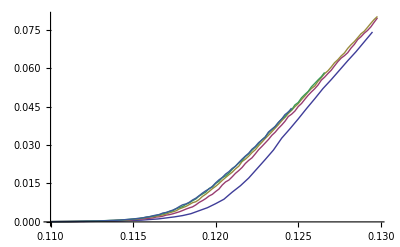

```mathematica
v=6;
n=2;
ListLinePlot[{gap[2][v][n],gap[5][v][n],gap[10][v][n],gap[20][v][n],gap[30][v][n]}]
```